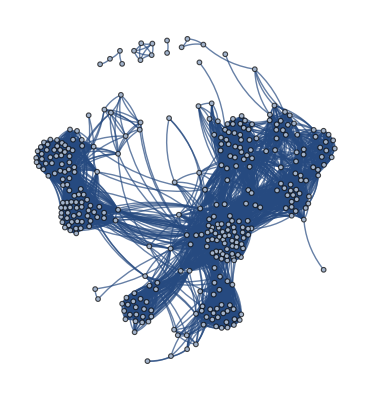

```mathematica
$graph=Import["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/graphCDK069.wxf"]
```

```mathematica
colorCommunities[graph_]:=HighlightGraph[$graph,Map[Subgraph[graph,#]&,FindGraphCommunities[$graph]]]
```

```mathematica
$fingerprintData=Import["/Users/joshuakhorsandi/Documents/Summer Research - 2023/WSS 2023/Chem Space - #225/ChemicalSpaceNetworks/ChemicalSpaceNetworks/Data/fingerprintDataCDK069.wxf"];
```

```mathematica
DynamicModule[
{vertexClicked={},graph=$graph,edges=EdgeList[$graph],vertices=Union@@List@@@EdgeList[$graph],bioType="pIC50",bioData=False,emb="GravityEmbedding",clickable=False},
plotLegend=Row[{BarLegend[{defaultBioToColor,{4,11}},6],Rotate[bioType,90Degree]}];
defaultVertexStyle=#->defaultBioToColor[$fingerprintData[#,bioType]]&;
vertexCoordinates=GraphEmbedding[$graph];vertexSize=EuclideanDistance[vertexCoordinates[[1]],vertexCoordinates[[2]]];
Panel[
Column[{
Row[{
ActionMenu["Communities",{
"Highlight":>(graph=colorCommunities[graph]),
"Export":>Export["communities.wxf",FindGraphCommunities[graph]]
}],
ActionMenu["Connected components",{
"Highlight":>(graph=HighlightGraph[graph,ConnectedComponents[graph]]),
"Export":>Export["connectedComponents.wxf",ConnectedComponents[graph]]
}],
ActionMenu["Subgraph",{
"Generate from selected":>(graph=Subgraph[graph,vertexClicked,VertexStyle->Automatic]),
"Export":>(Export[StringJoin[{"subgraph",vertexClicked,".wxf"}],graph])
}],
ActionMenu["Adjacency Matrix",{
"Export":>(Export["graphAdjMatrix.wxf",WeightedAdjacencyMatrix[graph]]),
"Export Spectra":>(Export["adjMatrixSpectra.wxf",Eigenvalues[WeightedAdjacencyMatrix[$graph]]])
}],
ActionMenu["Switch Embedding",{
"Spring Electrical":>(graph=Annotate[graph,GraphLayout->"SpringElectricalEmbedding"];emb="SpringElectrical")
}],
ActionMenu["Representative Molecule",{
"Show Plot":>CreateDialog[MoleculePlot[$fingerprintData[First@Part[VertexList[graph],Ordering[DegreeCentrality[graph],All,Greater]],"Molecule"]]],
"Highlight":>(graph=HighlightGraph[graph,First@Part[VertexList[graph],Ordering[DegreeCentrality[graph],All,Greater]]])
}],
ActionMenu["Reset",{
"Graph":>(graph=$graph),
"Selected":>(vertexClicked={}),
"BioData":>(bioData=False;graph=First@graph;graph=Annotate[graph,VertexStyle->Automatic]),
"All":>(graph=$graph;vertexClicked={})
}]
}],
Row[{
Button["Select Vertices",
clickable=Not[clickable];If[clickable,graph=Annotate[graph,VertexShapeFunction->
(EventHandler[Disk[#1,0.05],
"MouseClicked":>(If[CurrentValue["ShiftKey"],
vertexClicked=Join[vertexClicked,First@ConnectedComponents[graph,#2]];graph=Annotate[graph,VertexStyle->Thread[vertexClicked->Red]],
vertexClicked=Append[vertexClicked,#2];graph=Annotate[graph,VertexStyle->Thread[vertexClicked->Red]]]
)]&)];,
graph=Annotate[graph,VertexShapeFunction->Automatic]];],
Button["Show distances",(graph=Annotate[graph,EdgeLabels->"EdgeWeight"])],
Button["Show Molecules",
(graph=Annotate[graph,VertexShapeFunction->({pos,v,size}|->Inset[MoleculePlot[$fingerprintData[v,"Molecule"]],pos,Center,20*size])
])],
Button["Show Bio Data",
bioData=Not[bioData];
If[bioData,
graph=Annotate[graph,VertexStyle->defaultVertexStyle/@vertices]//Legended[#,plotLegend]&]],
Button["Draw Edge Weights",graph=graph//
IGEdgeMap[Identity,"weight"->IGEdgeProp[EdgeWeight]]/*
IGEdgeMap[Directive[AbsoluteThickness[9 #1]]&,EdgeStyle->{IGEdgeProp["weight"]}]]
}],
Panel[Dynamic[graph],Alignment->Center]
},Alignment->Center]
]
]
```